# Building and Training Basic Neural Networks

## Wolfram Research training@wolfram.com

© Wolfram Research, Inc.

## Overview

### Network Data

Neural networks are built up using tensors. So the first step is to convert different data types to tensors.

Tensors

Encoders and Decoders

### Network Structure

Layers

Network Constructors

### Network Training

This section focuses on training the networks in an optimized fashion.

Basic Theory

Loss Layers

### Performing Logistic Regression on Real-World Data

Basic Layers

Network Construction

Accuracy Estimation

### LeNet Trained on Handwritten Digits

This section of the talk focuses on logistic regression using neural networks for classification and training the LeNet (Yann LeCun) on handwritten digits. For each of the examples, each layer, encoders/decoders and constructors are considered.

Basic Layers

Network Construction

Accuracy Estimation

## Network Data: Tensors

### Ranks of Tensors

Tensors are multidimensional arrays.

Rank 0 (scalars): 0.0

Rank 1 (vectors): {0.0, 1.0}

Rank 2 (matrices): {{1.,2.,3.} , {3., 2., 1.}}

Rank-n tensors: {... {... {1., 2., 3.}...}...}

### Examples of Tensors:

Vectors as coordinates of points:

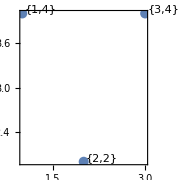
-Graphics-  ≈ ( | 1 |  | 4 | )
( | 3 |  | 4 | )
( | 2 |  | 2 | )

```mathematica
data={{1,4},{3,4},{2,2}};
plot=ListPlot[Labeled[#,Framed[#,FrameStyle->None]]&/@data,Frame->True,LabelStyle->Medium,AspectRatio->1,PlotRangePadding->1,PlotStyle->PointSize[0.04],ImageSize->Small];
gr=Grid[{{Style["(",20],Style[1,20],Spacer[1],Style[4,20],Style[")",20]},{Style["(",20],Style[3,20],Spacer[1],Style[4,20],Style[")",20]},{Style["(",20],Style[2,20],Spacer[1],Style[2,20],Style[")",20]}}];Row[{plot, Spacer[60], Style["  ≈ ",32], Spacer[60], gr}]
```

Matrices as grayscale images:

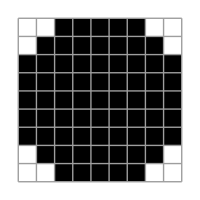
-Graphics-  ≈ (0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0
0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0
0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0)

```mathematica
Row[{ArrayPlot[DiskMatrix[4],Mesh->All,ImageSize->200], Spacer[60], Style["  ≈ ",32], Spacer[60], MatrixForm@DiskMatrix[4]}]
```

Rank-3 tensors as a colored image:

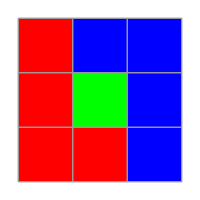
-Graphics-  ≈ ((1 | 0 | 0
1 | 0 | 0
1 | 1 | 0) | (0 | 0 | 0
0 | 1 | 0
0 | 0 | 0) | (0 | 1 | 1
0 | 0 | 1
0 | 0 | 1))

```mathematica
re={1,0,0};bl={0,0,1};gr={0,1,0};data={{re,bl,bl},{re,gr,bl},{re,re,bl}};img=Image[data];Row[{ArrayPlot[ImageData@img,ColorFunction->RGBColor,Mesh->True,ImageSize->200], Spacer[60], Style["  ≈ ",32], Spacer[60],MatrixForm[{MatrixForm/@Round[Transpose[data,{2,3,1}]]}]}]
```

## Network Data: Encoders and Decoders

#### Class Encoders and Decoders

Encode the user-defined class (here the class of male and females):

```mathematica
enc=NetEncoder[{"Class",{"male","female"}}]
```

Use it to create the input tensor:

```mathematica
enc[{"male","female","female"}]
```

Create the decoder for the same classes:

```mathematica
dec=NetDecoder[{"Class",{"male","female"}}]
```

Use a probabilistic approach to decode the output (make sure each of the tensors to be decoded follows the dimension specification of the decoder):

```mathematica
dec[{{1.9,1.9},{0.9,0.7}}]
```

### Image Encoder

```mathematica
image= -Graphics-;
```

```mathematica
enc=NetEncoder[{"Image",ImageDimensions[image],ColorSpace->"Grayscale"}]
```

```mathematica
encoded=enc[image];
```

```mathematica
dec=NetDecoder[{"Image",ColorSpace->"Grayscale"}]
```

```mathematica
dec[encoded]
```

## Layers

A neural network is a biologically inspired model and consists of “layers” in between the input and output tensors.

The implemented layers in the Wolfram Language™ are the following:

```mathematica
CellPrint[ExpressionCell[
table={{"Basic Layers ","LinearLayer | ElementwiseLayer | SoftmaxLayer"},{"Elementwise Computation Layers","ElementwiseLayer | ThreadingLayer  | ConstantTimesLayer  | ConstantPlusPlayer"},
{"Convolution and Filtering Layers","ConvolutionLayer | DeconvolutionLayer | PoolingLayer | ResizeLayer |  SpecialTransformationLayer"},
{"Training optimization Layers","ImageAugmentationLayer | BatchNormalizationLayer | DropoutLayer | LocalResponseNormalizationLayer | InstanceNormalizationLayer"},{"Structure Manipulation Layers","CatenateLayer | FlattenLayer | ReshapeLayer | ReplicateLayer |  PaddingLayer | PartLayer | TransposeLayer"},{"Array Operation Layers","ConstantArrayLayer | SummationLayer | TotalLayer | AggregationLayer | DotLayer"},{"Recurrent Layers","BasicRecurrentLayer |  GatedRecurrentLayer | LongShortTermMemoryLayer"},
{"Sequence-Handling Layers","EmbeddingLayer | SequenceLastLayer | SequenceReverseLayer | SequenceMostLayer | SequenceRestLayer | SequenceAttentionLayer | UnitVectorLayer"}};
Grid[Prepend[table,{"Layer Type","Layers"}],Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.8]}}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Alignment->Left,Spacings->{4,2}],"Output",GeneratedCell->False]]
```

Layer Type | Layers
Basic Layers  | LinearLayer | ElementwiseLayer | SoftmaxLayer
Elementwise Computation Layers | ElementwiseLayer | ThreadingLayer  | ConstantTimesLayer  | ConstantPlusPlayer
Convolution and Filtering Layers | ConvolutionLayer | DeconvolutionLayer | PoolingLayer | ResizeLayer |  SpecialTransformationLayer
Training optimization Layers | ImageAugmentationLayer | BatchNormalizationLayer | DropoutLayer | LocalResponseNormalizationLayer | InstanceNormalizationLayer
Structure Manipulation Layers | CatenateLayer | FlattenLayer | ReshapeLayer | ReplicateLayer |  PaddingLayer | PartLayer | TransposeLayer
Array Operation Layers | ConstantArrayLayer | SummationLayer | TotalLayer | AggregationLayer | DotLayer
Recurrent Layers | BasicRecurrentLayer |  GatedRecurrentLayer | LongShortTermMemoryLayer
Sequence-Handling Layers | EmbeddingLayer | SequenceLastLayer | SequenceReverseLayer | SequenceMostLayer | SequenceRestLayer | SequenceAttentionLayer | UnitVectorLayer

## Network Constructors

#### NetChain

NetChain can be used to connect different layers in a chain-like fashion to create a neural net.

Create a simple chain performing logistic regression:

```mathematica
net=NetChain[{LinearLayer[],ElementwiseLayer[LogisticSigmoid]}]
```

#### NetGraph

NetGraph can be used to connect different layers to create a graphical neural network.

Concatenating output from intermediate layers:

```mathematica
net=NetGraph[{Ramp,LogisticSigmoid,CatenateLayer[]},{1->2,{1,2}->3}]
```

### NetPort

NetPort represents the specified port for a layer in a NetGraph or similar structure.

Creating a simple total NetGraph with two inputs:

```mathematica
net=NetGraph[{Ramp,LogisticSigmoid,TotalLayer[]},{NetPort["Input1"]->1,NetPort["Input2"]->2,{1,2}->3}]
```

## Network Training: Basic Theory

### Neural Networks Learn on Training Data

Neural networks are data-driven algorithms.

You can think of training data as implicitly specifying a function, where training “tunes” a net to approximate this function.

### Basic Theory

Training a network finds a (local) optimum of the loss as a function of the learned parameters.

To train one parameter x, the error or loss ϵ of the network is computed on subsets (batches) of the training data. The chain rule is used to back-propagate the error ϵ through the network.

Updating the parameter x→x- r ∂x is known as gradient descent with learning rate r. Here is an example that shows how the error (cost function) is minimized with respect to the two parameters, using gradient descent.

The parameters of the network gradually converge on a local optimum, i.e. the error is minimized.

In practice, more complicated update schemes like ADAM are used.

The aim of the training (optimization) is to:

•   Evaluate the vector of class scores f, that is a function of the initial weights and inputs, given, the dataset of pairs of input and class,
•  Minimize the loss function, L, which comprises of regularization loss and data loss.
•  The data loss computes the differences between the scores f and the labels y (given by Loss Layers in the Wolfram Language). 
•  The regularization loss is only a function of the weights or the parameters


So the question now is:
a) How do we initialize the weights? 
b) What method to use for parameter updates?
c) What hyperparameter to use?

NetInitialize

Answers a) How to initialize the parameters?
 
NetIntiailize[net] gives a net in which all uninitialized learnable parameters in net have been given initial values. By default, all methods initialize bias vectors to zero.

-Graphics-

◻  Random : 
•   Initialize the weights of the neurons to small numbers to break symmetry.
•  Assures that they are unique 
• You can separately initialize the weight matrices and vectors using the suboptions present
W ∝ RandomVariate[NormalDistribution[0,0.1/0.01]]

-Graphics-


◻  Identity: 
• In the above approach outputs from a randomly initialized neuron has a variance that grows with the number of inputs. 
• Normalize the variance of each neuron’s output to 1 by scaling its weight vector by the square root of the number of inputs. 
• Initialize the net using the "Identity" method, which results in a net that attempts to preserve the components of tensors as they pass through linear layers
W ∝ RandomVariate[UniformDistribution[-1/√n_in,1/√n_in]] 

◻  Xavier

W ∝ RandomVariate[UniformDistribution[-r,r]] 
-Graphics-
 http : // machinelearning.wustl.edu/mlpapers/paper_files/AISTATS2010_GlorotB10.pdf (Xavier et.al)
Tanh:  RandomVariate[UniformDistribution[-r,r]] ;  r =√(6/(n_in+n_out))
Sigmoid:  RandomVariate[UniformDistribution[-r,r]] ;  r =4 √(6/(n_in+n_out))
https://arxiv.org/pdf/1502.01852v1.pdf (He. et.al)
ReLU:  RandomVariate[UniformDistribution[-r,r]] ;  r =√(2/n_in)

◻  Orthogonal: 
•  First initialize the weight matrix, then perform SingularValueDecomposition. 
•  W_init = RandomReal[{0,0.1}, {n,m}]; {W_fin,w,v} = SingularValueDecomposition[W_init ]; W_fin is your required weight

NetTrain: Methods

Answers b) What method to use for parameter update?

Stochastic Gradient Descent: 

◻  Vanilla Update (not used in the Wolfram Language, here only for teaching purpose) : 
•  Update parameters in the negative direction of the gradient. 
•  Parameters x and the gradient dx, form used is: x += - learning_rate * dx

◻  Momentum Update (not used in the Wolfram Language, here only for teaching purpose) : : 
•  Better convergence for rates on deep networks. 
• The update has the form: 
v = μ * v - learning_rate*dx  # integrate velocity
x += v  # integrate position

Here we see an introduction of a v variable that is initialized at zero, and an additional hyperparameter μ, which is entered in the Wolfram Language (as Momentum)

-Graphics-
◻  Nesterov Momentum Update:  In this method of updating the momentum, we are looking one-step ahead, and as a result we have a little bit better guess for the step (SGD in Wolfram Language)
v_prev = v # back this up
v = μ * v - learning_rate * dx # velocity update stays the same
x += - μ * v_prev + (1 + μ) * v # position update changes form

◻  AdaGrad:  http://www.jmlr.org/papers/volume12/duchi11a/duchi11a.pdf

cache += dx**2
x += - learning_rate * dx / (Sqrt(cache) + ϵ)
The smoothing term ϵ (~1e-4 to 1e-8) avoids division by zero. 

◻  RMSProp: Geoff Hinton’s Coursera class http://www.cs.toronto.edu/~tijmen/csc321/slides/lecture_slides_lec6.pdf (Slide 29)
(RMSProp in Wolfram Language)
cache += Beta* cache + (1 - Beta) * dx**2
x += - Beta * dx / (Sqrt(cache) + ϵ)
Here, Beta is a hyperparameter and typical values are [0.9, 0.99, 0.999].

◻  Adam: https://arxiv.org/pdf/1412.6980.pdf
(Adam in Wolfram Language)
m = Beta1*m + (1-Beta1)*dx
v = Beta2*v + (1-Beta2)*(dx**2)
x += - learning_rate * m / (Sqrt(v) + ϵ)
Recommended values in the paper are ϵ = 1e-8, beta1 = 0.9, beta2 = 0.999.

NetTrain: Regularization and Hyperparameter Optimization

Regularization

It refers to a process of introducing additional information in order to solve an ill-posed problem or to prevent over fitting. As a result of regularization, the total loss function gets modified to include the data loss as well as the regularization loss. There are different ways you can obtain regularization for your neural networks:

◻ L2 Regularization:
•    For all weighs ω in the network, we add the term 1/2λ ω^2  to the objective, where λ is the regularization strength. 
•   Heavily penalizes peaky weight vectors and preferring diffuse weight vectors. 

◻  Gradient and Weight Clipping 

◻  Network Layers specific for regularization (e.g. DropoutLayer) 

Hyperparameter Optimization

Neural networks training involve many hyperparameter settings. The most common hyperparameters include:

▪ the initial learning rate 
▪ learning rate decay schedule (such as the decay constant)
▪ regularization strength (L2 penalty)

Certain aspects of hyperparameter optimization are:

Hyperparameter ranges: A typical sampling of the learning rate would look as follows: learning_rate = 10^UniformDistribution(-6, 1)
Random Search: http://www.jmlr.org/papers/volume13/bergstra12a/bergstra12a.pdf 
It is better to search randomly than on grid.

In the Wolfram Language, the hyperparameters can be obtained from suboptions for methods:
-Graphics-

## Loss Layers

### Loss Layer Types

The loss layer specifies the functional form of loss to be computed, which measures the compatibility between a prediction (e.g. the class scores in classification) and the actual value of the label. The data loss takes the form of an average over the data losses for every individual example. In the iteration of training the network, this explicit loss function is minimized by tuning the parameters (via back propagation). The implemented loss layers are as follows:

MeanAbsoluteLossLayer: represents a loss layer that computes the mean absolute difference between the "Input" port and "Target" port (Poisson type used for regression problem):

```mathematica
data=<|"Input"->{1,2,3},"Target"->{3,2,1}|>;MeanAbsoluteLossLayer[][data]
meanAbsoluteLoss=N[Mean[Flatten[Abs[#Input-#Target]]]]&;
meanAbsoluteLoss[data]
```

MeanSquaredLossLayer: represents a loss layer that computes the mean squared difference between the "Input" port and "Target" port (Gaussian type used for regression problem):

```mathematica
data=<|"Input"-> {1,2,3},"Target"->{3,2,1}|>;
MeanSquaredLossLayer[][data]
meanSquaredLoss=N[Mean[Flatten[(#Input-#Target)^2]]]&; 
meanSquaredLoss[data]//N
```

CrossEntropyLossLayer: represents a net layer that computes the information-theoretic distance by comparing probabilities with specified target values (used for classification problem):

```mathematica
ceLoss=-Total[#Target*Log@#Input]&;data=<|"Input"-> {0.1,0.2,0.7},"Target"->{0.1,0.3,0.6}|>;
ceLoss[data]
CrossEntropyLossLayer["Probabilities"][data]
```

When a loss layer is chosen automatically for a port, the loss layer to use is based on the layer within the net whose output is connected to the port. For SoftmaxLayer and LogisticSigmoid, CrossEntropyLossLayer is chosen; for non-loss layers, MeanSquaredLossLayer is chosen. If a loss layer is specified, it is used unchanged.

## Performing Logistic Regression with Real-World Data: Basic Layers

### LinearLayer

A LinearLayer is essentially an affine transformation x → Ax + b, where A is the “weight matrix” and the vector b is the “bias vector”. This type of layer has a lot of parameters, and hence is used toward the end of the network (after the dimensions of the tensor have been reduced). To understand the LinearLayer, it is easiest to construct a net with a single LinearLayer, which is solving a simple linear approximation:

```mathematica
data={2,10,3};
layer=NetInitialize@LinearLayer[2,"Input"-> 3]
layer[data]
```

```mathematica
linear[data_, weight_,bias_]:=Dot[weight,data]+bias
```

```mathematica
linear[data, NetExtract[layer,"Weights"],NetExtract[layer,"Biases"]]
```

### ElementwiseLayer

The ElementwiseLayer applies a unary function f to every element of the input tensor. The function f is referred to as the activation function in the literature; commonly used activation functions are LogisticSigmoid, Tanh and Ramp (Rectified Linear Unit, ReLU):

```mathematica
Row[Table[
{min,max}={-1,1}*If[f===Ramp,1,3];
Plot[f[x],{x,min,max},PlotLabel->f,ImageSize->300,Frame->True,PlotRange->{{min,max},{-1,1}},AspectRatio->0.5,FrameTicks->{{{-1,0,1},{}},{{min,0,max},{}}}],{f,{LogisticSigmoid,Tanh, Ramp}}], Spacer[180]]
```

```mathematica
elem=ElementwiseLayer[Tanh];data=RandomReal[{0,10},10];elem[data]
```

As expected, it applies Tanh to the data:

```mathematica
Tanh[data]
```

### SoftmaxLayer

The softmax classifier takes an input (a vector) and returns normalized class probabilities. The element x_i in a vector is converted to e^x_i/∑_j e^x_j, and generally the innermost dimension is used as the normalization dimension.

Apply the SoftmaxLayer on a list of random data to get probabilistic interpretations. On a list:

```mathematica
data=RandomReal[{0,10},10];
{SoftmaxLayer[]@data,Total@SoftmaxLayer[]@data}
```

See what SoftmaxLayer is actually evaluating by using the functional approach:

```mathematica
fsoftmax[x_]:=N@Exp[x]/Total[Exp[x],{-1}];
{fsoftmax[data],Total@fsoftmax[data]}
```

## Performing Logistic Regression with Real-World Data: Constructing the Network

This example uses the Titanic dataset to perform logistic regression with both categorical and numerical input data. The dataset contains information for the passengers traveling on the Titanic: the class of travel, their age, their gender and if they survived or not.

Get the data from the Wolfram server, delete incomplete entries, and split the data into a training and a test dataset:

```mathematica
titanicdata=ExampleData[{"Dataset","Titanic"}];
titanicdata=DeleteMissing[titanicdata,1,2];
{trainingData,testData}=TakeDrop[RandomSample@titanicdata,800]
```

In the next step, encoders for each of the features are created: class (with 3 values), sex (with 2 values) and survived can use the built-in Boolean encoder:

```mathematica
classEncoder=NetEncoder[{"Class",{"1st","2nd","3rd"}, "UnitVector"}]
genderEncoder=NetEncoder[{"Class",{"male","female"},"UnitVector"}]
```

Combine all the input from the different class encoders, label the input ports, and connect to the first layer:

```mathematica
net1=NetGraph[{CatenateLayer[]},{{NetPort["class"],NetPort["age"],NetPort["sex"]}->1},"class"-> classEncoder,"age"->"Scalar","sex"-> genderEncoder]
```

In the second step, the layers that perform the logistic regression are added. Take the already existing NetGraph that was built for inputting the layers and add the necessary layers for logistic regression. Connect the LogisticSigmoid to the appropriate decoder so that it outputs a Boolean to indicate if the passenger survived or not:

```mathematica
net2=NetGraph[{net1,LinearLayer[],LogisticSigmoid},{1->2->3->NetPort["survived"]},"survived"->"Boolean"]
```

## Performing Logistic Regression with Real-World Data: Training, Predicting and Accuracy

Train the network using NetTrain. MaxTrainingRounds is specified as an option to specify how many times the data is revisited. As the training progresses, you can see the training progress report that shows the update and displays the error function:

```mathematica
trained=NetTrain[net2,trainingData,MaxTrainingRounds->1000]
```

Once the network is trained, you can enter the input features for fictitious passengers and find the probability for their survival:

```mathematica
{trained[<|"class"-> "1st","age"->20,"sex"->"female"|>],trained[<|"class"-> "1st","age"->20,"sex"->"female"|>,None]}
{trained[<|"class"-> "3rd","age"->30,"sex"->"male"|>],trained[<|"class"-> "3rd","age"->30,"sex"->"male"|>,None]}
```

You can take a further step and plot the probability of survival with age for all the variations in class and gender:

```mathematica
p[class_,age_,sex_]:=trained[<|"class"->class,"age"->age,"sex"->sex|>,None];
Plot[{p["1st",x,"female"],p["2nd",x,"female"],p["3rd",x,"female"],p["1st",x,"male"],p["2nd",x,"male"],p["3rd",x,"male"]}, {x,0,100},PlotLegends->{"female, 1st class", "female, 2nd class","female, 3rd class", "male, 1st class","male, 2nd class", "male, 3rd class"}, Frame->True,FrameLabel-> {"age (years)", "survival probability"}]
```

Assess the accuracy of the network by testing it against the test dataset created. Compare the accuracy with the built-in Classify function:

```mathematica
cm=ClassifierMeasurements[trained,testData-> "survived","Accuracy"]
```

```mathematica
cf=Classify[trainingData->"survived"];
ClassifierMeasurements[cf,testData->"survived","Accuracy"]
```

## LeNet explained

LeNet is a simple convolution network that performs feature extraction that can be used to classify an image:

```mathematica
NetChain[
{

(*STEP 1: FETAURE EXTRACTION*)

(*FIRST CONVOLUTION BLOCK*) 
ConvolutionLayer[20,3],     (*first convolution => 20 feature images*)
ElementwiseLayer[Ramp],     (*activation function (ReLU) => non-linearity, sparsity*)
(*FIRST POOLING BLOCK*)
PoolingLayer[2,2],          (*max pooling => downsampling*)
(*SECOND CONVOLUTION BLOCK*) 
ConvolutionLayer[50,3],     (*second convolution => 50 feature images*)
ElementwiseLayer[Ramp],     (*activation function (ReLU) => non-linearity, sparsity*)
(*SECOND POOLING BLOCK*)
PoolingLayer[2,2],          (*max pooling => downsampling*)

FlattenLayer[],             (*flattening => images to vector*)

(*STEP 2: COMPUTING CLASS PROBABILITY*)

(*FULLY-CONNECTED BLOCK 1*)
LinearLayer[500],          (*first fully connected layer => feature vector from image features*)
ElementwiseLayer[Ramp],    (*activation function (ReLU) => non-linearity, sparsity*)

(*FULLY-CONNECTED BLOCK 2*)
LinearLayer[10],           (*second fully connected layer => class prediction*)
(*PROBABILITY COMPUTATIONS*)
SoftmaxLayer[]              (*normalization*)
},

"Input"  -> NetEncoder[{"Image", {32, 32}}],  (*encoder => image to tensor*)
"Output" -> NetDecoder[{"Class", classes}]  (*decoder => tensor to class*)
];
```

## LeNet: Network Training (with Options and Properties)

### Network Data

In this example, LeNet is trained on the handwritten digits from the MNIST database. In the Wolfram Language database, the digits are classified into training and test datasets. ResourceData can be used to access the data:

```mathematica
trainingData=ResourceData[ResourceObject["MNIST"],"TrainingData"];
testData=ResourceData[ResourceObject["MNIST"],"TestData"];
```

### Constructing the Network

```mathematica
lenet=NetChain[{
ConvolutionLayer[20,5],Ramp,PoolingLayer[2,2],
ConvolutionLayer[50,5],Ramp,PoolingLayer[2,2],
FlattenLayer[],500,Ramp,10,SoftmaxLayer[]},
"Output"->NetDecoder[{"Class",Range[0,9]}],
"Input"->NetEncoder[{"Image",{28,28},"Grayscale"}]
]
```

### Training the Network, with Various Options

Train the network now on the training data (with different options to make the process faster):

If a simple NetTrain is performed, you will see that the training takes approximately 40 minutes:

```mathematica
trained=NetTrain[lenet,trainingData]
```

Try to improve the speed by changing the number of MaxTrainingRounds to 2 (reduces training time by a factor of 5) and changing the BatchSize, which in turn improves the number of inputs per second:

```mathematica
trained=NetTrain[lenet,trainingData,MaxTrainingRounds->2,BatchSize->512 ]
```

Finally, if you have a GPU, the training goes much faster; in this case the training completes in 20s:

```mathematica
trained=NetTrain[lenet,trainingData,MaxTrainingRounds->2,BatchSize->512,TargetDevice->"GPU" ]
```

### Obtaining Different Properties

```mathematica
cm=ClassifierMeasurements[trained,testData]
```

```mathematica
cm["ConfusionMatrixPlot"]
```

```mathematica
cm["Accuracy"]
```

```mathematica
{lossPlot,weightPlot,gradPlot}=NetTrain[lenet,trainingData,Automatic,{"LossEvolutionPlot","RMSWeightEvolutionPlot","RMSGradientEvolutionPlot"},MaxTrainingRounds->2,BatchSize->512,TargetDevice->"GPU"];
```

```mathematica
Column[{lossPlot,weightPlot,gradPlot}]
```

### Exporting a Trained Net

```mathematica
Export["testnet.wlnet",trained]
```

```mathematica
trained=Import["testnet.wlnet"]
```

```mathematica
cm=ClassifierMeasurements[trained,testData]
```

```mathematica
cm["Accuracy"]
```

## Glossary

BatchSize | CatenateLayer | CellAnnotation | Class | ClassifierMeasurements
Classify | ColorSpace | ConfusionMatrixPlot | ConvolutionLayer | DeleteMissing
Dot | ElementwiseLayer | ExampleData | Exp | Flatten
FlattenLayer | Frame | FrameLabel | Image | ImageDimensions
Input | LinearLayer | LogisticSigmoid | LossEvolutionPlot | MaxTrainingRounds
Mean | MeanAbsoluteLossLayer | MeanSquaredLossLayer | N | NetChain
NetDecoder | NetEncoder | NetExtract | NetInitialize | NetPort
Output | Plot | PlotLegends | PoolingLayer | Ramp
RandomReal | RandomSample | ResourceData | ResourceObject | RMSGradientEvolutionPlot
RMSWeightEvolutionPlot | SoftmaxLayer | TakeDrop | Tanh | Target
TargetDevice | Total | TotalLayer |  |